Quit

# Inits

```mathematica
Get["/Users/astrumia/Dropbox/ProgrammiMiei/Feynman diagrams/HEP/LogLogTicks.m"];DGreen=Darker@Green;
```

### Costanti numeriche

```mathematica
Clear[Convert,Natural,NNatural,Meter,GeV,MeV,TeV,eV,barn,Parsec,Joule,Kilogram,Gram,Kelvin,erg,LightYear,cm,km,millimeter,Year,Month,kyr,Coulomb,Ampere,Tesla];
Natural[x_]:=x//.{barn-> 10^-28 Meter^2,pb->10^-40 Meter^2,nb->10^-37 Meter^2,fb->10^-43 Meter^2,
 gram->kg/1000,kg->Kilogram,sec->Second,GeV->10^9 eV,
MeV ->10^6 eV,meV ->10^-3 eV,TeV ->10^12 eV,Parsec->3.085677580 10^16 Meter,Mpc->10^6 Parsec,
LightYear->0.9461 10^16 Meter,Year->3.1557 10^7 Second,kyr->1000 Year,Month->Year/12,
cm->Meter/100,km->1000 Meter,millimeter->Meter/1000,
Newton->Kilogram *Meter/Second^2,erg->10^-7 Joule,
Second->299792458. Meter,Meter->1/(1.9732696 10^-7 eV),Kelvin->0.0000861735 eV,Kilogram-> 10^36 eV/1.782661731,Gram->Kilogram/1000,Joule->10^19 eV/1.602176462,
Ampere->Coulomb/Second,
Tesla->Newton/(Ampere Meter)};
Convert[x_,units_]:=Natural[x/units]units;
InUnits[x_,units_]:=Natural[x/units];
```

### Inits: generic cross section for bound state formation

Define Sommerfeld as analytically computed from the Hulthen approximation to the Yukawa potential.  
Definitions:  ζ = α/vrel;  ϵ = M_V/(M_DMα) ,  v_rel= 2β

```mathematica
κS=1.74;Clear[Sommerfeld];
Sommerfeld[0,ϵ_]:=1; Sommerfeld[x_,0]:=(-π x)/(1-Exp[π x]);
Sommerfeld[x_,ϵ_]:=(π x Sinh[(-2 π)/(Abs[ϵ x] κS)])/(Cosh[(2 π)/(Abs[x ϵ] κS)]-Cosh[(2π √(1+Abs[ϵ] Sign[x] x^2 κS))/(Abs[x ϵ] κS)]); 
Sommerfeld[β_,α_,MV_,M_]:=Sommerfeld[α/β,-MV/(M α)];
```

λi è il fattore α_eff=λ α per tenere conto del Sommerfeld nello stato iniziale.

```mathematica
σvbsf[ζ_,λi_,{λf_,Spin_,1,0},CJ_,Cτ_]:=σ0 1/2 1/gχ^2(2 Spin+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+λf^2 ζ^2)^3)(CJ+Cτ/λf)^2;
σvbsf[ζ_,λi_,{λf_,Spin_,2,0},CJ_,Cτ_]:=σ0 1/2 1/gχ^2(2 Spin+1)(2^15 π)/3(( ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])  ζ^5 λf^3 λi (1+ζ^2 λi^2) (CJ λf (4-ζ^2 λf (λf-2 λi))+Cτ (4+ζ^2 λf (-3 λf+4 λi)))^2 )/( (1-ⅇ^(-2 π ζ λi)) (4+ζ^2 λf^2)^5));
σvbsf[ζ_,λi_,{λf_,Spin_,2,1},CJ_,Cτ_]:=σ0(4096 ⅇ^(-4 ζ λi ArcCot[(ζ λf)/2]) π (1+2 Spin) ζ^7 λf^5 λi (32 (2 Cτ+CJ λf)^2 (1+ζ^2 λi^2) (4+ζ^2 λi^2)+(CJ (-12 λi+λf (8+ζ^2 (3 λf-4 λi) λi))+Cτ (4+ζ^2 (-3 λf^2+12 λf λi-8 λi^2)))^2))/(9 (1-ⅇ^(-2 π ζ λi)) gχ^2 (4+ζ^2 λf^2)^5);
```

SM parameters

```mathematica
vev=174.;MZ=91.187;MW=80.38;ccW=MW^2/MZ^2;ssW=1-ccW;MPl=1.221 10^19;ndofSM=106.75;
g2MZ=Sqrt[2]MW/vev;α2MZ=g2MZ^2/(4π);
gYMZ=g2MZ Sqrt[ssW/ccW];αYMZ=gYMZ^2/(4π);αemZ=ssW α2MZ;
sQ[x_]:=If[x>0,x^2,0];
α3MZ=0.118;g3MZ=Sqrt[4π α3MZ];
```

### Thermal average and masses

Thermal masses

```mathematica
Clear[ssWT,MWT,MZT,MγT,MgT];Tc=155.;Rvev[T_]:=Re[Sqrt[1-T^2/Tc^2]];vevT[T_]:=vev*Rvev[T];
MWTSU2[T_]:=MW Rvev[T];
MgT[T_]:=Sqrt[2]g3MZ T;
MWT[T_]:=Sqrt[MW^2 Rvev[T]^2+11/6 g2MZ^2 T^2];
root[T_]:=√(121 (g2MZ^2-gYMZ^2)^2 T^4+66 (g2MZ^2-gYMZ^2)^2 T^2 vevT[T]^2+9 (g2MZ^2+gYMZ^2)^2 vevT[T]^4);
MZT[T_]:=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)+root[T])];
MγT[T_]:=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)-root[T])];
ssWT[T_]:=1/2-((g2MZ^2-gYMZ^2) (11 T^2+3 vevT[T]^2))/(2 root[T]); (* ssWT[0] = ssW;  ssWT[T>Tc] = 0 *)
```

```mathematica
ΔMT[T_]:=164.80/161.17 α2MZ/2(ssWT[T] (MZT[T]-MγT[T])+(MWT[T]-MZT[T]));
```

```mathematica
ztab=Table[10^lz,{lz,1,4,0.1}];zmax=Max[ztab];zmin=Min[ztab];
ThermalAverage[state_,SU3]:=(Clear[β,z];integrand= β^2  Exp[-z β^2] σv[state]/σ0/.vrel->2β;
βmax=5/Sqrt[z];Table[σ0(4 z^(3/2))/(√π)NIntegrate[integrand ,{β,0,Min[βmax,1]}],{z,ztab}]);
```

```mathematica
θf[x_]:=If[x>0,x,0];
ThermalAverage[state_,SU2]:=(Clear[β,z];If[NumberQ[state],{i,n,ℓ}=IntegerDigits[state];λf=λ[i];αeff=λf α2MZ;
EBinding=αeff^2 MDM/(4 n^2)θf[1-1.74 n^2 MWT[MDM/z]/(αeff MDM)-1.61 n^2(MWT[MDM/z]/(αeff MDM))^2 ℓ(ℓ+1)]^2;

ω=EBinding+MDM β^2;Rkω=Re[Sqrt[1-(MW Rvev[MDM/z]/ω)^2]];
βmin=Re[Sqrt[MW Rvev[MDM/z]-EBinding]]/MDM;  (* valore tale che ω = MW(T) *)
VectorMassSuppression=Rkω(1-Rkω^2/3)3/2+αemZ/(3 α2MZ);,VectorMassSuppression=1;βmin=0;];
integrand=VectorMassSuppression* β^2  Exp[-z β^2] σv[state]/σ0/.vrel->2β;

βmax=5/Sqrt[z];
Table[σ0(4 z^(3/2))/(√π)NIntegrate[integrand ,{β,βmin,Max[βmin,Min[βmax,1]]}],{z,ztab}]);
```

```mathematica
DefineState[state_]:=(Clear[z];If[NumberQ[state]&&group==SU2,
{i,n,ℓ}=IntegerDigits[state];thisMV=MWT[MDM/z];
S=Which[(EvenQ[(i-1)/2]&&EvenQ[ℓ])||(OddQ[(i-1)/2]&&OddQ[ℓ]),0,(EvenQ[(i-1)/2]&&OddQ[ℓ])||(OddQ[(i-1)/2]&&EvenQ[ℓ]),1,True,Print["State ",state," not allowed"]];
decaysto=100 i+10(n-1);αeff=α2MZ λ[i]];
If[group==SU3,{i,S,n,ℓ}=state;thisMV=MgT[MDM/z];decaysto={i,1-S,1,0};αeff=α3MZ λ[i]];
gdof[state]=dim[i]*(2S+1)*(2ℓ+1);
EBQ[state,z_]:=Evaluate[1-1.74 n^2 thisMV/(αeff MDM)-1.61 n^2(thisMV/(αeff MDM))^2 ℓ(ℓ+1)];
EB[state,z_]:=Evaluate[αeff^2 MDM/(4 n^2)EBQ[state,z]^2];
If[ℓ==0,BR[state,z_]:=If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ^2 MDM^3)/gdof[state](σvTI[state][z])/(Γann[state]+10^-100))^-1,0]];
If[ℓ==1,
BR[state,z_]:=BR[Evaluate[decaysto],z]*If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ^2 MDM^3)/gdof[state](σvTI[state][z])/(Γdecay[state]+10^-100))^-1,0]];
RσvTeff[state,z_]:=σvTI[state][z]BR[state,z]/σ0;);
```

# Run

## Vari

```mathematica
Table[ClebschGordan[{2,m1},{2,m2},{0,0}] ,{m1,-2,2},{m2,-2,2}]//MatrixForm
```

### Compute numerically binding energies for a Yukawa potential

Work in the basis of the Coulomb potential

```mathematica
Clear[r,n,l,x,M];μ=M/2;aμ=1/(α μ);
Rnl[n_,l_]:=√((2/(n aμ))^3((n-l-1)!)/(2n ((l+n)!))) Exp[-r/(n aμ)] ((2r)/(n aμ))^l LaguerreL[n-l-1,2 l+1, (2r)/(n aμ)];
ψ[n_,l_,m_]:=Rnl[n,l]*SphericalHarmonicY[l,m,θ,φ]//PowerExpand
ψ[n_,l_,m_]:=Rnl[n,l]*SphericalHarmonicY[0,0,θ,φ]//PowerExpand
Table[ψ[n,0,0],{n,1,3}]
Hψ[n_,l_,m_]:=Simplify[-1/(2μ)(1/r^2 D[r^2 D[ψ[n,l,m],r],r])- (α/r-(l(l+1))/(M r^2))ψ[n,l,m]];
```

{(ⅇ^(-1/2 M r α) M^(3/2) α^(3/2))/(2 √(2 π)),(ⅇ^(-1/4 M r α) M^(3/2) α^(3/2) (2-(M r α)/2))/(16 √π),(ⅇ^(-1/6 M r α) M^(3/2) α^(3/2) (54-18 M r α+M^2 r^2 α^2))/(324 √(6 π))}

Check normalization

```mathematica
nmax=3;l=1;
Table[4π  Integrate[r^2 ψ[n1,l,0]  ψ[n2,l,0],{r,0,∞},GenerateConditions->False] ,{n1,l+1,nmax},{n2,l+1,nmax}]
```

{{1,0},{0,1}}

```mathematica
nmax=3;l=1;
Table[Integrate[r^2 Rnl[n1,l]  Rnl[n2,l],{r,0,∞},GenerateConditions->False] ,{n1,l+1,nmax},{n2,l+1,nmax}]
```

{{1,0},{0,1}}

Check Hamiltonian

```mathematica
nmax=3;l=1;H0=Table[4π  Integrate[r^2 Hψ[n1,l,0]  ψ[n2,l,0] ,{r,0,∞},GenerateConditions->False] ,{n1,l+1,nmax},{n2,l+1,nmax}]
```

{{-(M α^2)/16,0},{0,-(M α^2)/36}}

Compute the matrix elements of Yukawa - Coulomb

```mathematica
Clear[livelli,n,l];{nmax,lmax}={10,6};Do[E0=-(M α^2)/4;
H0=Table[If[n1==n2,-(M α^2)/(4 n1^2),0],{n1,l+1,nmax},{n2,l+1,nmax}];
aH0=H0/E0;MV=ϵV M α;
δH=Table[4π  Integrate[-α(Exp[- MV r]-1)/(r E0)r^2 ψ[n1,l,0]  ψ[n2,l,0]/.{M->1,α->1} ,{r,0,∞},GenerateConditions->False] ,{n1,l+1,nmax},{n2,l+1,n1}];
aδH=MapThread[Join,{δH,Rest/@Flatten[δH,{{2},{1}}]}];
ϵVtab=Table[10^lϵ,{lϵ,-3,Log[10,1/κ],0.01}];
eigs=Transpose[Table[-Sort[-Eigenvalues[aH0+aδH]],{ϵV,ϵVtab}]];
Do[livelli[n,l]=Transpose[{Log[10,ϵVtab],n^2 eigs⟦n-l⟧}];
EnI=Interpolation[livelli[n,l]];ϵmax[n,l]=10^lϵ/.FindRoot[EnI[lϵ]==0,{lϵ,-1}];
If[n<4,Print["Level ",{n,l}," exists at ϵ < ",ϵmax[n,l]]];
,{n,l+1,nmax}],{l,0,lmax}]
```

Level {1,0} exists at ϵ < 0.585515

Level {2,0} exists at ϵ < 0.152746

Level {3,0} exists at ϵ < 0.0683768

Level {2,1} exists at ϵ < 0.110082

Level {3,1} exists at ϵ < 0.0562786

Level {3,2} exists at ϵ < 0.0456536

```mathematica
1/ϵmax[2,0]/4
```

1.63671

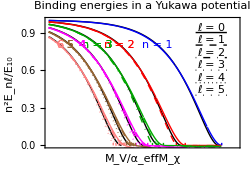

```mathematica
style[n_,l_]:={{Blue,Red,Darker@Green,Magenta,Brown,Pink}⟦n⟧,{Dashing[{10,0}],Dashed,DotDashed,Dotted,Dashing[{0.001,0.01}],Dashing[{0.001,0.02}]}⟦l+1⟧};
plot=Show[nmax=6;θ[x_]:=If[x>0,x^2,Null];κ=1/ϵmax[1,0];κ=1.9;
Hulthen=Plot[Evaluate[Table[θ[1-n^2 κ  10^lϵ],{n,1,nmax}]],{lϵ,-3,Log[10,1/κ]},PlotStyle->{{Thin,Black}},Frame->True,FrameTicks->LogLinTicks[dettaglio1],FrameLabel->{"M_V/α_effM_χ","n^2E_nℓ/E_10"},PlotRange->{{-3,0},{0,1}},AspectRatio->0.7],
Graphics[Flatten[Table[{style[n,l],Line[livelli[n,l]],Dashing[{1,0}],Line[{p={Log[10,ϵmax[n,l]],0},p+{0,0.02}}],Text[If[n<4,"n = "<>ToString[n],n],{xx/.FindRoot[Interpolation[livelli[n,0]][xx]==0.8,{xx,-1}],0.8},{0,0},{1,-1},Background->White]},{n,1,nmax},{l,0,n-1}]],PlotRangeClipping->True,PlotRange->{0,1}],
Graphics[Flatten[Table[{style[1,l],Black,Line[p={-0.4,0.9-0.1l};{p-{0.25,0},p+{0.25,0}}],Text["ℓ = "<>ToString[l],p+{0,0.04}]},{l,0,nmax-1}]]],
PlotLabel->"Binding energies in a Yukawa potential",ImageSize->250]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/YukawaEbinding.pdf",plot]
```

/Users/astrumia/Dropbox/DM bound state/figs/YukawaEbinding.pdf

#### Fit of the energy levels to a fit function

{2477,4}

Fit:  E ≈ E_10(1-1.74076 n^2 ϵ-1.60552 l (1+l) n^2 ϵ^2)^2   ;   χ^2 = 0.49509

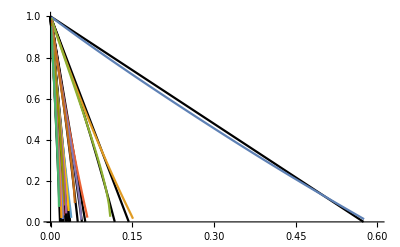

1.42165

```mathematica
nmax=5;livellis[n_,l_]:=Select[livelli[n,l],#⟦2⟧>0&]/.{lϵ_,Eb_}:>{n,l,10^lϵ,Sqrt[Eb]-1};
data=Flatten[Table[livellis[n,l],{n,1,nmax},{l,0,n-1}],2];data//Dimensions
Clear[n,ϵ,l];fit=Fit[data,{n^2 ϵ, n^2 ϵ^2 l(l+1)},{n,l,ϵ}];
Print["Fit:  E ≈ E_10",(1+fit)^2,"   ;   χ^2 = ",Sum[{n,l,ϵ,Eb}=this;(Eb-fit)^2,{this,data}]];
Show[Plot[Table[1+fit,{n,1,nmax},{l,0,n-1}],{ϵ,0,0.6},PlotStyle->Black,PlotRange->{{0,0.6},{0,1}}],ListLinePlot[Flatten[Table[livellis[n,l],{n,1,nmax},{l,0,n-1}],1]/.{n_,l_,ϵ_,Eb_}:>{ϵ,Eb+1},PlotRange->All],PlotRange->{{0,0.6},{0,1}}]
```

#### Obsolete plot

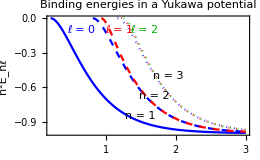

```mathematica
fp[x_]:=If[x<0,x,Null];
r=-n^2(fp[-6+(n)^2 π^2 x+12 n^3 l  π^2 x^3]^2)/(36 n^2)/.x->10^-y;
plot=Plot[{r/.{n->1,l->0},r/.{n->2,l->0},r/.{n->3,l->0},r/.{n->2,l->1},r/.{n->3,l->1},r/.{n->3,l->2}},{y,0,3},
PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},{Red,Dashed},{Red,Dotted},{Darker@Green,Dotted}},
Frame->True,FrameLabel->{"α_effM_χ/M_V","n^2E_nℓ"},PlotRange->{{0,2},{0.01,-1}},
Epilog->{Black,Text["n = 1",{1.5,-0.85}],Text["n = 2",{1.7,-0.675}],Text["n = 3",{1.9,-0.5}],Blue,Text["ℓ = 0",{0.65,-0.1}],Red,
Text["ℓ = 1",{1.2,-0.1}],Darker@Green,Text["ℓ = 2",{1.55,-0.1}]},PlotLabel->"Binding energies in a Yukawa potential",ImageSize->260]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/YukawaEbinding.pdf",plot]
```

/Users/astrumia/Dropbox/DM bound state/figs/YukawaEbinding.pdf

### Bound-state wave functions for a Hulthen potential

```mathematica
ClearAll[RH,qH,Norma,αeff];
RH[n_,l_]:=Norma[n,l] ⅇ^(-MV q[n,l] r κ)((1-ⅇ^(-MV r κ))^(1+l))/r JacobiP[-1-l+n,2 q[n,l],1+2 l,1-2 ⅇ^(-MV r κ)];
EBH[n_,l_]:=αeff^2 MDM/(4 n^2)(1- n^2(κ MV)/(MDM αeff))^2;
qHXX[n_,l_]:=Sqrt[MDM EB[n,l]]/(κ MV);
qH[n_,l_]:=(MDM αeff (1-(MV n^2 κ)/(MDM αeff)))/(2 MV n κ);
Norma[n_,0]:=Sqrt[κ MV (1-n^4 y^2)/(2 y^3 n^5)];Norma[n_,1]:=Norma[n,0]Sqrt[(1-n^2 y^2)/((n^2-1) n^2 y^2)];
```

Check normalizations

```mathematica
tab=Table[uno=Integrate[r^2 RH[n,0]^2,{r,0,∞},GenerateConditions->False]/.q->qH/.αeff->(MV κ)/(MDM y)//Simplify,{n,1,5}]//Simplify
```

{1,1,1,1,1}

```mathematica
tab=Table[uno=Integrate[r^2 RH[n,1]^2,{r,0,∞},GenerateConditions->False]/.q->qH/.αeff->(MV κ)/(MDM y)//Simplify,{n,2,4}]//Simplify
```

{1,1,1}

Check orthonromality

```mathematica
zero=Integrate[r^2 RH[2,0]RH[1,0],{r,0,∞},GenerateConditions->False]/.q->qH/.αeff->(MV κ)/(MDM y)//Simplify
```

0

```mathematica
zero=Integrate[r^2 RH[3,1]RH[2,1],{r,0,∞},GenerateConditions->False]/.q->qH/.αeff->(MV κ)/(MDM y)//Simplify
```

0

### Free-state wave function for a Hulthen potential

```mathematica
Somm=(2π αeff Sinh[π MDM vrel/(κ MV)])/(vrel(Cosh[π MDM vrel/(κ MV)]-Cosh[π MDM vrel/(κ MV) Sqrt[1-(4αeff κ MV)/(MDM vrel^2)]]));
{ap,am}=(1+l){1,1}+ⅈ*MDM*vrel/(2 κ MV)({1,1}+{1,-1}Sqrt[1-(4αeff κ MV)/(MDM vrel^2)]);
RH=Sqrt[Somm]/(Sqrt[(2l+1)/(4π)](2l)!αeff)((1-ⅇ^(-κ MV r))^(l+1))/(MDM r)ⅇ^(-1/2 I MDM r vrel)Hypergeometric2F1[am,ap,2(l+1),1-ⅇ^(-κ MV r)]Sqrt[sProduct[k^4+(MDM^2 αeff^2)/(MV^2 κ^2)+k^2 (MDM^2 vrel^2)/(MV^2 κ^2)(1-(2 MV αeff κ)/(MDM vrel^2)),{k,0,l}]];

RC=Sqrt[4π(2l+1)] Abs[Gamma[l+1-I αeff/vrel]]/Gamma[2l+2] Exp[(π αeff)/(2vrel)- I p  r](2 p r)^l Hypergeometric1F1[l+1+ I αeff/vrel,2(l+1),2 I p r]/.p->MDM vrel/2;
NRH={RH,RC}/.l->0/.sProduct->Product/.MDM->10000./.αeff->1/10./.MV->0.07/.vrel->0.2/.κ->1/7//Chop;
NRH/.r->0.001//Chop
```

{2.98927,2.98927}

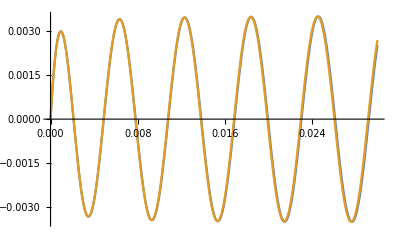

```mathematica
NRH={RH,RC}/.l->0/.sProduct->Product/.MDM->10000./.αeff->1/10./.MV->80/.vrel->0.2/.κ->1/7//Chop;Plot[Evaluate[Re[r NRH]],{r,0,0.03}]
```

Check that it reduces to the known free limit (see https://en.wikipedia.org/wiki/Partial_wave_analysis)

```mathematica
Clear[RFree];Rfree[l_]:=Sqrt[4π (2l+1)] SphericalBesselJ[l,MDM vrel r/2 ];
Check1=Table[(Series[Series[RH/.sProduct->Product,{αeff,0,0}],{MV,0,0}]//Normal//Expand//PowerExpand//ExpToTrig)/Normal[Series[Rfree[l],{r,∞,2}]]//Simplify,{l,0,2}]
```

{1,1,1}

```mathematica
Check1=Table[Series[Series[RH/.sProduct->Product,{αeff,0,0}],{MV,0,0}]//Normal//Expand//PowerExpand//ExpToTrig//Simplify,{l,0,0}]
```

{(4 √π Sin[(MDM r vrel)/2])/(MDM r vrel)}

```mathematica
Normal[Series[SphericalBesselJ[0,p r ],{r,∞,2}]]
```

Sin[p r]/(p r)

```mathematica
Table[SphericalHarmonicY[l,0,θ,φ]/(Sqrt[(2l+1)/(4π)]LegendreP[l,Cos[θ]]),{l,0,3}]
```

{1,1,1,1}

### Milne relation

```mathematica
Clear[T];nDMeq=gDM ( (MDM T)/(2π))^(3/2)Exp[-MDM/T];
nIeq=gI ( (2MDM T)/(2π))^(3/2)Exp[-MB/T];
γI=nDMeq^2/2 σvbsf;Γbreak=γI/nIeq/.MB->2MDM -EB//PowerExpand//Simplify
```

(ⅇ^(-EB/T) gDM^2 MDM^(3/2) T^(3/2) σvbsf)/(16 gI π^(3/2))

### Boltzmann equation for 2 states

```mathematica
γeff=Collect[(γ1 (RDM^2-R1)+γ2(RDM^2-R2))/(RDM^2-1)/.First[Solve[{Γ1br (RDM^2-R1)+Γ1ann(1-R1)+Γ12(R2-R1)==0,Γ2br (RDM^2-R2)+Γ2ann(1-R2)+Γ12(R1-R2)==0},{R1,R2}]],{γ1,γ2},Simplify]
```

(γ2 ((Γ1ann+Γ1br) Γ2ann+Γ12 (Γ1ann+Γ2ann)))/((Γ1ann+Γ1br) (Γ2ann+Γ2br)+Γ12 (Γ1ann+Γ1br+Γ2ann+Γ2br))+(γ1 (Γ12 (Γ1ann+Γ2ann)+Γ1ann (Γ2ann+Γ2br)))/((Γ1ann+Γ1br) (Γ2ann+Γ2br)+Γ12 (Γ1ann+Γ1br+Γ2ann+Γ2br))

```mathematica
Collect[γeff/.{Γ2ann->0},{γ1,γ2},Simplify]
```

(Γ12 Γ1ann γ2)/((Γ1ann+Γ1br) Γ2br+Γ12 (Γ1ann+Γ1br+Γ2br))+(γ1 Γ1ann (Γ12+Γ2br))/((Γ1ann+Γ1br) Γ2br+Γ12 (Γ1ann+Γ1br+Γ2br))

```mathematica
Series[(Γ12 Γ1ann γ2)/((Γ1ann+Γ1br) Γ2br+Γ12 (Γ1ann+Γ1br+Γ2br)),{Γ12,0,1}]//Normal//Simplify
```

(Γ12 Γ1ann γ2)/((Γ1ann+Γ1br) Γ2br)

```mathematica
α2
```

### Check Boltzmann solution via the boundary layer method

```mathematica
Clear[gχ,M,T];s=(2 π^2)/45 gSM T^3;
neq=gχ ( (M T)/(2π))^(3/2)Exp[-M/T];
neq/s/.T->M/z//PowerExpand
```

(45 ⅇ^-z gχ z^(3/2))/(4 √2 gSM π^(7/2))

```mathematica
zf==Log[(2 gχ S[zf] λBoltz)/((2 π)^(3/2) zf^(1+1/2))]
```

30.8106==Log[7.80113×10^11 S[30.8106]]

z_f = 20.5241  Y = {1.89064,1.95706} * 10^-10    :  ratio = 0.966062

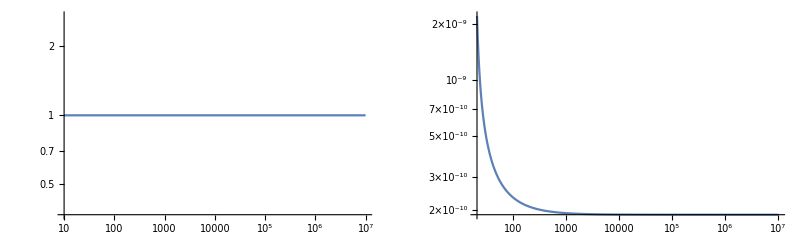

```mathematica
{zmin,zmax}={10,10^7};S[z_]:=1+ 0 0.1  z^2  Exp[-z/100]; λBoltz=10^11;gχ=6;gSM=106.75;Yeq[z_]:=(45 ⅇ^-z gχ z^(3/2))/(4 √2 gSM π^(7/2));
ComputeY:=(Ysol=Y/.First@NDSolve[{Y'[z]==-λBoltz S[z]/z^2(Y[z]^2-Yeq[z]^2),Y[zmin]==Yeq[zmin]},Y,{z,zmin,zmax},AccuracyGoal->20];Ysol[zmax]);
ComputeY;zf=zf/.FindRoot[zf==Log[ (2gχ S[zf] λBoltz)/(2π zf)^(3/2)],{zf,25}];
Print["z_f = ",zf,"  Y = ", 10^10{num=Ysol[zmax],approx=1/λBoltz(S[zf]/zf^2+NIntegrate[S[z]/z^2,{z,zf,zmax}])^-1}," * 10^-10    :  ratio = ",num/approx];GraphicsRow[{LogLogPlot[S[z],{z,zmin,zmax}],LogLogPlot[Ysol[z],{z,zf,zmax},PlotRange->All]}]
```

```mathematica
S[z_]:=1+ 0.001  z^2  Exp[-z/200];n1=ComputeY;a1=1/(6 S[zf]/zf^2+NIntegrate[S[z]/z^2,{z,zf,zmax}]);
S[z_]:=1+2  0.001  z^2  Exp[-z/200];n2=ComputeY;a2=1/(6 S[zf]/zf^2+NIntegrate[S[z]/z^2,{z,zf,zmax}]);
{n2/n1,a2/a1}
```

{0.564126,0.563687}

```mathematica
Clear[S,λ];DSolve[Y'[z]== -λ/z^2 S[z] Y[z]^2,Y[z],z]
```

{{Y[z]→1/(-C[1]-∫_1^z -(λ S[K[1]])/K[1]^2ⅆK[1])}}

## Sommerfeld

### Inits: Sommerfeld thermal average per Houlthen and Ω_DM

Define Sommerfeld as analytically computed from the Hulthen approximation to the Yukawa potential.  
Definitions:  x = α/β;  ϵ = M_V/(M_DMα) ,  peaks when ϵ = 1/κn^2  v_rel= 2β

```mathematica
κS=1.8;Clear[Sommerfeld];
Sommerfeld[0,ϵ_]:=1; Sommerfeld[x_,0]:=(-π x)/(1-Exp[π x]);Sommerfeld[x_,0.]:=(-π x)/(1-Exp[π x]);
Sommerfeld[x_,ϵ_]:=(π x Sinh[(-2 π)/(Abs[ϵ x] κS)])/(Cosh[(2 π)/(Abs[x ϵ] κS)]-Cosh[(2π √(1+Abs[ϵ] Sign[x] x^2 κS))/(Abs[x ϵ] κS)]); 
Sommerfeld[β_,α_,MV_,M_]:=Sommerfeld[α/β,-MV/(M α)];
```

Thermal average  SommerfeldT[α*Sqrt[z],ϵ] where   z = M/T  and Kin = Mβ^2.  
The integral need to go to β>1 since I fix M=T=1 and assume the rescaling
Needs a few minutes

```mathematica
T=1;M=1;Clear[α,SommerfeldT,ϵ];αtab=Table[10^x,{x,-1,3,0.2}];αtab=Sort[Join[-αtab,αtab]];
ϵtab=Join[{0},Table[10^i,{i,-2,1,0.01}]]; (* it's critical that is is thin enough *)
Stab=Flatten[Table[{α,ϵ,(4 M^(3/2))/(√π T^(3/2))NIntegrate[β^2  Exp[-M β^2/T]Sommerfeld[α/β,ϵ] ,{β,0,4}]},{α,αtab},{ϵ,ϵtab}],1];
SommerfeldT=Interpolation[Stab,InterpolationOrder->1];
```

InterpolatingFunction[{{-1000., 1000.}, {0., 10.}}, <>]

### Some plots about Sommerfeld and its thermal average

```mathematica
Plot[{Evaluate[Sommerfeld[1,α,0,1]],Evaluate[Sommerfeld[1,α,1,1]],Evaluate[Sommerfeld[1,α,2,1]]},{α,-10,10},PlotStyle->{Red,Dashed,Dotted},Frame->True,FrameLabel->{"α/β","S"}]
```

```mathematica
Plot3D[Log[10,SommerfeldT[α,e]],{α,-1000,1000},{e,0,2}]
```

```mathematica
Plot[SommerfeldT[-1000,e],{e,0,1},Epilog->Table[Line[{{1/(κS n^2),0},{1/(κS n^2),1000}}],{n,1,6}]]
```

```mathematica
Plot[Evaluate[Table[SommerfeldT[α,e],{e,0,1,0.1}]],{α,-100,100}]
```

### Ω_DM for the 3-plet

```mathematica
Clear[n];σvrel=(g2^4(2 n^4+17 n^2-19))/(256π *(2n)MDM^2)/.g2->Sqrt[4π α2]/.n->{3,5}
```

{(37 π α2^2)/(12 MDM^2),(207 π α2^2)/(20 MDM^2)}

Use the approximated solution to the Boltzmann equations

```mathematica
Clear[Rσv,σv];σ0=37/12 π α2MZ^2/MDM^2;
Rσv[MV_,zf_]:=16/111 SommerfeldT[-2 α2MZ Sqrt[zf],MV/(MDM 2 α2MZ)]+75/111 SommerfeldT[-α2MZ Sqrt[zf],MV/(MDM α2MZ)]+20/111 SommerfeldT[α2MZ Sqrt[zf],MV/(MDM α2MZ)];
Clear[ΩDMhh];MDMtab=Table[m,{m,100.,3500,10}];gχ=6;
ΩDMhhtabSom=Table[λBoltz= σ0 MDM MPl  √(ndofSM π/45) ;Clear[zf];zmax=10^7;
MVz[z_]:=Sqrt[11/6 4π α2MZ( MDM/z)^2+MZ^2 Rvev[MDM/z]^2];
zf=zf/.FindRoot[zf==Log[2gχ Rσv[MVz[zf],zf] λBoltz/((2π)^(3/2)Sqrt[zf])],{zf,25}];
YDM=1/λBoltz/(NIntegrate[Rσv[MVz[z],z]/z^2,{z,zf,zmax},Method->{Automatic,"SymbolicProcessing"->0}]+Rσv[MVz[zf],zf]/zf^2);
NΩDMhh=0.110 MDM YDM/(0.40 10^-9);
{MDM/1000,NΩDMhh},{MDM,MDMtab}];
```

```mathematica
ΩDMhhtab0=Table[λBoltz= σ0 MDM MPl  √(ndofSM π/45) ;Clear[zf];zmax=10^6;
zf=zf/.FindRoot[zf==Log[  (2gχ λBoltz)/((2π)^(3/2)Sqrt[zf])],{zf,25}];
YDM=1/λBoltz/(NIntegrate[1/z^2,{z,zf,zmax},Method->{Automatic,"SymbolicProcessing"->0}]+1/zf^2);
NΩDMhh=0.110 MDM YDM/(0.40 10^-9);
{MDM/1000,NΩDMhh},{MDM,MDMtab}];
```

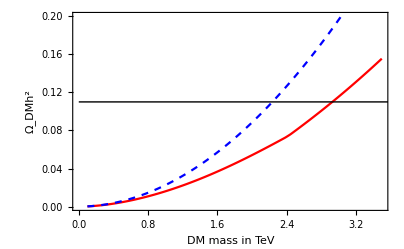

```mathematica
ListLinePlot[{ΩDMhhtabSom,ΩDMhhtab0},PlotRange->{0,0.2},Frame->True,FrameLabel->{"DM mass in TeV","Ω_DMh^2"},PlotStyle->{Red,{Dashed,Blue}},Epilog->Line[{{0,0.110},{15,0.110}}]]
```

It peaks at 2 TeV, not at 2.5 ?? ??

```mathematica
MDMpeak=κS MZ/(2α2MZ)
```

2416.34

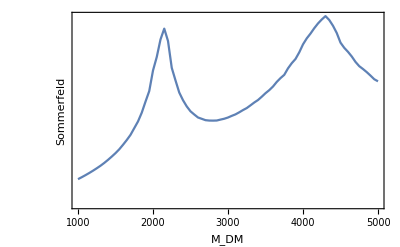

```mathematica
ListLinePlot[Table[{MDM,Log[10,Rσv[MW,10^6]]},{MDM,1000,5000,50}],Frame->True,FrameTicks->LinLogTicks[normale],FrameLabel->{"M_DM","Sommerfeld"}]
```

### Ω_DM for the 5-plet

Use the instantaneous decoupling approximation

Use the approximated solution

```mathematica
σ0=207/20 π α2MZ^2/MDM^2;zf=25.;
MVz[z_]:=Sqrt[11/6 4π α2MZ( MDM/z)^2+MZ^2 Rvev[MDM/z]^2];
Rσv[MV_,zf_]:=16/69 SommerfeldT[-6 α2MZ Sqrt[zf],MV/(MDM 6 α2MZ)]+25/69 SommerfeldT[-5 α2MZ Sqrt[zf],MV/(MDM 5 α2MZ)]+28/69 SommerfeldT[-3α2MZ Sqrt[zf],MV/(MDM 3 α2MZ)];
σv[MV_,zf_]:=σ0*Rσv[MV,zf];
```

At z > 10^4 it is affected by the T=0 mass and it depends a lot on its precise value that shifts the position of 0-energy bound states.
Apart from this, at smaller z it agrees with the numeric code

```mathematica
LogLogPlot[{1,Rσv[MVz[z],z]/.MDM->11500},{z,1,10^7}];
Rσv[MVz[z],z]/.MDM->11500/.z->10^3
Plot[Rσv[MVz[z],z]/.z->10^5,{MDM,500,11000}];
```

16.6264

```mathematica
Clear[ΩDMhh];MDMtab=Table[m,{m,100.,12000,200}];gχ=10;
ΩDMhhtabSom=Table[λBoltz= σ0 MDM MPl  √(ndofSM π/45) ;Clear[zf];zmax=10^3;MVz[z_]:=Sqrt[11/6 4π α2MZ] MDM/z;
zf=zf/.FindRoot[zf==Log[2gχ Rσv[MVz[zf],zf] λBoltz/((2π)^(3/2)Sqrt[zf])],{zf,25}];
YDM=1/λBoltz/(NIntegrate[Rσv[MVz[z],z]/z^2,{z,zf,zmax},Method->{Automatic,"SymbolicProcessing"->0}]+Rσv[MVz[zf],zf]/zf^2);
NΩDMhh=0.110 MDM YDM/(0.40 10^-9);
{MDM/1000,NΩDMhh},{MDM,MDMtab}];
ΩDMhhtab0=Table[λBoltz= σ0 MDM MPl  √(ndofSM π/45) ;Clear[zf];zmax=10^6;
zf=zf/.FindRoot[zf==Log[  (2gχ λBoltz)/((2π)^(3/2)Sqrt[zf])],{zf,25}];
YDM=1/λBoltz/(NIntegrate[1/z^2,{z,zf,zmax},Method->{Automatic,"SymbolicProcessing"->0}]+1/zf^2);
NΩDMhh=0.110 MDM YDM/(0.40 10^-9);
{MDM/1000,NΩDMhh},{MDM,MDMtab}];
```

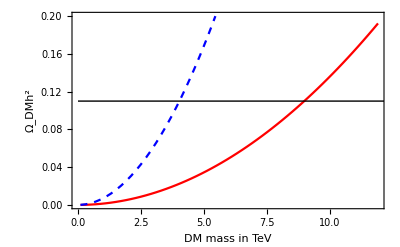

```mathematica
ListLinePlot[{ΩDMhhtabSom,ΩDMhhtab0},PlotRange->{0,0.2},Frame->True,FrameLabel->{"DM mass in TeV","Ω_DMh^2"},PlotStyle->{Red,{Dashed,Blue}},Epilog->Line[{{0,0.110},{15,0.110}}]]
```

```mathematica
ΩDMhhtabSom
```

{{0.1,0.0000148835},{0.3,0.000131292},{0.5,0.000361244},{0.7,0.000703562},{0.9,0.00115749},{1.1,0.00172247},{1.3,0.00239805},{1.5,0.00318386},{1.7,0.00407958},{1.9,0.00508494},{2.1,0.00619968},{2.3,0.00742359},{2.5,0.00875646},{2.7,0.0101981},{2.9,0.0117483},{3.1,0.013407},{3.3,0.015174},{3.5,0.0170491},{3.7,0.0190323},{3.9,0.0211233},{4.1,0.0233222},{4.3,0.0256286},{4.5,0.0280427},{4.7,0.0305642},{4.9,0.0331931},{5.1,0.0359292},{5.3,0.0387725},{5.5,0.0417229},{5.7,0.0447804},{5.9,0.0479447},{6.1,0.0512159},{6.3,0.0545938},{6.5,0.0580785},{6.7,0.0616698},{6.9,0.0653676},{7.1,0.069172},{7.3,0.0730828},{7.5,0.0770999},{7.7,0.0812234},{7.9,0.0854531},{8.1,0.089789},{8.3,0.094231},{8.5,0.0987791},{8.7,0.103433},{8.9,0.108193},{9.1,0.113059},{9.3,0.118031},{9.5,0.123109},{9.7,0.128293},{9.9,0.133582},{10.1,0.138977},{10.3,0.144477},{10.5,0.150083},{10.7,0.155795},{10.9,0.161612},{11.1,0.167535},{11.3,0.173563},{11.5,0.179696},{11.7,0.185935},{11.9,0.192279}}

### Indirect detection for the 5plet

WARNING : the SU(2)-invariant approximation is good only for finding the position of the peaks, all the rest fails

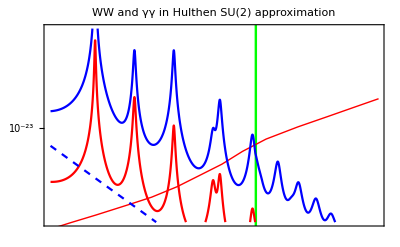

```mathematica
{σ1vWW,σ5vWW,σ1vγγ,σ5vγγ}={(40 π α2MZ^2)/MDM^2,(7 π α2MZ^2)/MDM^2,(20 π αemZ^2)/MDM^2,(14 π αemZ^2)/MDM^2};α2MZ=1/29.8;MW=80.2;β=10^-3;MZ=91.18;
σvWW=1/5 σ1vWW Sommerfeld[β,-6α2MZ,MW,MDM]+2/7 σ5vWW Sommerfeld[β,-3α2MZ,MW,MDM];
σvγγ=1/5 σ1vγγ Sommerfeld[β,-6α2MZ,MW,MDM]+2/7 σ5vγγ Sommerfeld[β,-3α2MZ,MW,MDM];
FERMIDwarfBound= (* on γ from DM DM -> WW *)Log[10,{{97.6408,2.67585*10^-26},{152.465,3.82738*10^-26},{242.041,5.64021*10^-26},{445.8,9.64841*10^-26},{707.715,1.42184*10^-25},{1303.49,2.43226*10^-25},{1874.26,3.37674*10^-25},{2927.27,5.60667*10^-25},{4497.72,1.01806*10^-24},{6468.82,1.69036*10^-24},{9305.35,3.16228*10^-24},{14063.8,5.74206*10^-24},{24655.2,1.04264*10^-23},{41815.9,1.73118*10^-23},{64233.,2.62839*10^-23},{101980.,4.1114*10^-23}}];
Plot[Evaluate[Log[10,InUnits[1/GeV^2,cm^3/Second]{σvWW,σvγγ,1/5 σ1vWW +2/7 σ5vWW }/.MDM->10^lm]],{lm,2.5,5},PlotPoints->100,
PlotRange->{-25,-20.9},PlotStyle->{Blue,Red,{Dashed,Blue},{Dashed,Red}},Prolog->{Green,Rectangle[{Log[10,11500],-30},{Log[10,12000],1}],Red,Line[FERMIDwarfBound]},Frame->True,FrameTicks->LogLogTicks[normale],PlotLabel->"WW and γγ in Hulthen SU(2) approximation"]
```

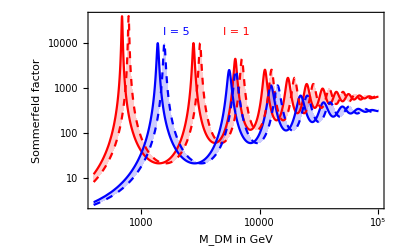

```mathematica
LogLogPlot[{Sommerfeld[β,-6α2MZ,MW,MDM],Sommerfeld[β,-3α2MZ,MW,MDM],Sommerfeld[β,-6α2MZ,MZ,MDM],Sommerfeld[β,-3α2MZ,MZ,MDM]},{MDM,400,100000},PlotStyle->{Red,Blue,{Dashed,Red},{Dashed,Blue}},Frame->True,
Filling->{1->{3},2->{4}},Epilog->{Red,Text["I = 1",Scaled[{0.5,0.9}]],Blue,Text["I = 5",Scaled[{0.3,0.9}]]},FrameLabel->{"M_DM in GeV","Sommerfeld factor"}]
```

## Binding energies

States with ell = 0 at T=0

```mathematica
Clear[n];MV=0.085;α2MZ=1/30.;
MDMtab=1.68 n^2 MV/({3,5,6}α2MZ)/.n->Range[1,5]
ListPlot[MDMtab,PlotRange->{1,25},Frame->True,FrameLabel->{"n","DM mass in TeV"}]
```

{{1.428,5.712,12.852,22.848,35.7},{0.8568,3.4272,7.7112,13.7088,21.42},{0.714,2.856,6.426,11.424,17.85}}

States at finite temperature

```mathematica
Clear[MDM,α2];g2=Sqrt[4π α2];
MV=Sqrt[11/6]g2 T;
Print["SU(2): λ > ",λ/.First@Solve[MDM==1.68 n^2 MV/(λ α2MZ),λ]/.α2->1/30./.T->MDM/25]
Clear[MDM,α2];g3=Sqrt[4π α3];
MV=Sqrt[2]g3 T;
Print["SU(3): λ > ",λ/.First@Solve[MDM==1.68 n^2 MV/(λ α3),λ]/.α3->0.118/.T->MDM/25];
```

SU(2): λ > 6.93548

SU(3): λ > 3.92291

Biding energies at finite temperature

```mathematica
Clear[Rvev,CalcolaMT,T];MW=80.2;Tc=155.;Rvev[T_]:=Re[Sqrt[1-T^2/Tc^2]];α2MZ=1/30.;g2MZ=Sqrt[4π α2MZ];α3MZ=0.118;αemMZ=1/129.;g3MZ=Sqrt[4π α3MZ];
MWT=Sqrt[MW^2 Rvev[T]^2+11/6 g2MZ^2 T^2];
MgT=Sqrt[2] g3MZ T;
θsq[x_]:=If[x<0,Null,x^2]
Eb[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.74 n^2 MV/(αeff Mχ)-1.61 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

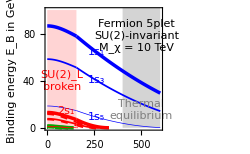

```mathematica
Mχ=10000.;
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005],Thickness[0.002]},{Blue,Red,{Red,Dashed},Darker@Green,{Darker@Green,Dashed},{Darker@Green,DotDashed}}],1];
{xmax,ymax}={600,100};
EBplot5=Plot[Evaluate[Table[{Eb[λ α2MZ,1,0,Mχ,MWT],Eb[λ α2MZ,2,0,Mχ,MWT],Eb[λ α2MZ,2,1,Mχ,MWT],Eb[λ α2MZ,3,0,Mχ,MWT],Eb[λ α2MZ,3,1,Mχ,MWT],Eb[λ α2MZ,3,2,Mχ,MWT]},{λ,{6,5,3}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{0,ymax},
Prolog->{Opacity[0.5],Lighter@Pink,Rectangle[{0,0},{Tc,100}],Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Gray,Text[Style["Thermal\nequilibrium",Small],{500,15}],Red,
Text[Style["SU(2)_L\nbroken",Small],{Tc/2,40}],Black,
Text["Fermion 5plet\nSU(2)-invariant\nM_χ = 10 TeV",{0.79 xmax,0.78ymax}],Blue,
Text[" 1s_1",{T,Eb[6 α2MZ,1,0,Mχ,MWT]}/.T->260,Background->White],
Text[" 1s_3",{T,Eb[5 α2MZ,1,0,Mχ,MWT]}/.T->260,Background->White],
Text[" 1s_5",{T,Eb[3 α2MZ,1,0,Mχ,MWT]}/.T->260,Background->White],Red,
Text[" 2s_1",{T,Eb[6 α2MZ,2,0,Mχ,MWT]+4}/.T->100]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{10,25,50,100}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/EB5.pdf",EBplot5]
```

/Users/astrumia/Dropbox/DM bound state/figs/EB5.pdf

Fermion 3 - plet

```mathematica
EBTnum={{3.06122,0.148343},{6.12245,0.148198},{9.18367,0.147023},{12.2449,0.145799},{15.3061,0.144504},{18.3673,0.143119},{21.4286,0.141623},{24.4898,0.139994},{27.551,0.138209},{30.6122,0.136244},{33.6735,0.134073},{36.7347,0.131668},{39.7959,0.129004},{42.8571,0.126056},{45.9184,0.122801},{48.9796,0.119222},{52.0408,0.115309},{55.102,0.11106},{58.1633,0.106486},{61.2245,0.101606},{64.2857,0.0964491},{67.3469,0.0910552},{70.4082,0.0854689},{73.4694,0.0797392},{76.5306,0.0739163},{79.5918,0.0680498},{82.6531,0.0621868},{85.7143,0.0563712},{88.7755,0.0506427},{91.8367,0.0450369},{94.898,0.0395857},{97.9592,0.0343175},{101.02,0.0292581},{104.082,0.0244322},{107.143,0.0198646},{110.204,0.0155829},{113.265,0.0116212},{116.327,0.00802646},{119.388,0.004871},{122.449,0.00227923},{125.51,0.000490931}};
```

QED binding energy < 0.0405625 GeV

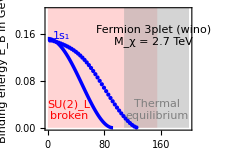

```mathematica
{xmax,ymax}={200,0.2};
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=2700.;Print["QED binding energy < ",αemMZ^2 Mχ/4," GeV"];
EBplot3=Plot[Evaluate[Table[{Eb[λ α2MZ,1,0,Mχ,MWT],Eb[λ α2MZ,2,0,Mχ,MWT],Eb[λ α2MZ,2,1,Mχ,MWT]},{λ,{2,1}}]],{T,0,100},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{{0,xmax},{0,ymax}},
Prolog->{Opacity[0.5],Lighter@Pink,Rectangle[{0,0},{Tc,100}],Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Blue,Table[Point[p],{p,EBTnum}],Gray,Text[Style["Thermal\nequilibrium",Small],{155,0.03}],Red,
Text[Style["SU(2)_L\nbroken",Small],{30,0.03}],Black,Text["Fermion 3plet (wino)\nM_χ = 2.7 TeV",{0.75xmax,0.78 ymax}],Blue,Text[" 1s_1",{T,0.02+Eb[2 α2MZ,1,0,Mχ,MWT]}/.T->20]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{15,25,50,100,300}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/EB3.pdf",EBplot3]
```

/Users/astrumia/Dropbox/DM bound state/figs/EB3.pdf

RINORMALIZZARE α3 AD ENRGIA PIU' BASSA

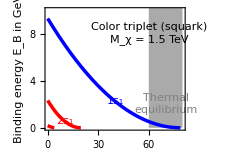

```mathematica
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=1500.;xmax=80;
EBplot=Plot[Evaluate[Table[{Eb[λ α3MZ,1,0,Mχ,MgT],Eb[λ α3MZ,2,0,Mχ,MgT],Eb[λ α2MZ,2,1,Mχ,MgT]},{λ,{4/3}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{{0,xmax},{0,10}},
Prolog->{Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Gray,Text[Style["Thermal\nequilibrium",Small],{70,2}],Black,Text["Color triplet (squark)\nM_χ = 1.5 TeV",{60,8}],Blue,Text[" 1s_1",{T,Eb[4/3 α3MZ,1,0,Mχ,MgT]}/.T->40,Background->White],Red,Text[" 2s_1",{T,Eb[4/3 α3MZ,2,0,Mχ,MgT]}/.T->10,Background->White]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{20,30,50,100,300}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/EB3c.pdf",EBplot]
```

/Users/astrumia/Dropbox/DM bound state/figs/EB3c.pdf

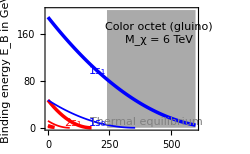

```mathematica
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=6000.;xmax=600;
EBplot8=Plot[Evaluate[Table[{Eb[λ α3MZ,1,0,Mχ,MgT],Eb[λ α3MZ,2,0,Mχ,MgT],Eb[λ α2MZ,2,1,Mχ,MgT]},{λ,{3,3/2}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{0,200},
Prolog->{Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,200}]},
Epilog->{Gray,Text[Style["Thermal equilibrium",Small],{400,10}],Black,
Text["Color octet (gluino)\nM_χ = 6 TeV",{450,160}],Blue,Text["1s_1",{T,Eb[3 α3MZ,1,0,Mχ,MgT]}/.T->200,Background->White],
Text["1s_8",{T,Eb[3/2 α3MZ,1,0,Mχ,MgT]}/.T->200,Background->White],Red,
Text["2s_1",{T,Eb[3 α3MZ,2,0,Mχ,MgT]}/.T->100,Background->White]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{10,20,30,50,200}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/EB8c.pdf",EBplot8]
```

/Users/astrumia/Dropbox/DM bound state/figs/EB8c.pdf

## Bound states

### Plot thermal effects

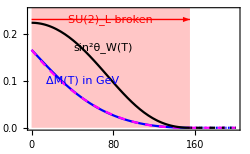

```mathematica
plotT=Plot[{ ΔMT[T],ΔMT[0]Re[(1-T/Tc)^(5/2)],ssWT[T]},{T,0,200},Frame->True,ImageSize->250,FrameLabel->{"Temperature T in GeV",""},PlotStyle->{Blue,{Magenta,Dashed},Black},Prolog->{Lighter@Lighter@Pink,Rectangle[{Tc,0},{0,200}]},
Epilog->{Black,Text["sin^2θ_W(T)",{70,0.17},{0,0},{1,-1}],Blue,Text["ΔM(T) in GeV",{50,0.10},{0,0},{1,-1}],
Red,Arrow[{{0,0.23},{Tc,0.23}}],Text[" SU(2)_L broken ",{Tc/2,0.23},Background->Lighter@Lighter@Pink]},PlotRange->{{0,200},{0,0.25}}]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/DMT.pdf",plotT]
```

/Users/astrumia/Dropbox/DM bound state/figs/DMT.pdf

```mathematica
Plot[{MWT[T],MZT[T],MγT[T]},{T,0,160}]
```

### 3plet

```mathematica
S=2;Clear[MDM];α^2(S α^3/2 MDM)(IR^2 dadj)/(S^2 dR)
```

15 MDM α^5

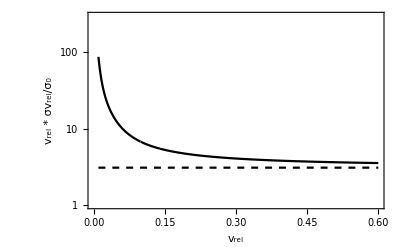

```mathematica
model="Fermion triplet (wino)";
ζ=α2MZ/vrel;dR=3;dadj=3;IR=2;Iadj=2;gχ=2 dR;MDM=2700;σ0=(π α2MZ^2)/MDM^2;Clear[σv];group=SU2;
Clear[dim];dim[i_]:=i;
 Somm[Isospin_]:=Sommerfeld[vrel/2,-λ[Isospin]α2MZ,MWT[MDM/z],MDM];
σv["ann"]=37/12 σ0;
σv["Sann"]=σv["ann"](16/111 Somm[1]+75/111 Somm[3]+20/111 Somm[5]);
Clear[λ,CJ,CT];λ[1]=2;λ[3]=1;λ[5]=-1; (* Coulomb strenghth factors for the various Isospin channels *)
Attributes[CJ]={Orderless};
CJ[1,3]=Sqrt[(IR dadj)/dR];CT[1,3]=Sqrt[(IR dadj Iadj^2)/(2*2 dR)];CT[3,1]=-CT[1,3];(* group factors for I = 1 ↔ 3 *)
CJ[5,3]=√(5/2);CT[5,3]=√10;(* group factors for I = 1 ↔ 3 *)
σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[110]=ssW/3 σvbsf[ζ,3->{1,0,1,0}];
Γann[110]=8 α2MZ^5 MDM; (* WRONG !!!! *)
Bstates={110};
LogPlot[Evaluate[1/σ0{σv["ann"],σv["Sann"]/.z->25,σv[110],σv[310]}],{vrel,0.01,0.6},FrameLabel->{"v_rel","v_rel * σv_rel/σ_0"},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,{"Tree s-wave","Sommerfeld σv","σv_110","σv_310","σv_510","σv_120","σv_320","σv_520","σv_121","σv_321","σv_521"}],Right],Frame->True,PlotRange->{1,300},PlotStyle->{{Black,Dashed},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted}}]
```

### 5plet

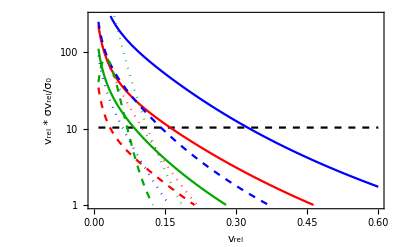

```mathematica
model="Fermion 5plet";ζ=α2MZ/vrel;dR=5;dadj=3;IR=10;Iadj=2;gχ=2 dR;
MDM=11500.;σ0=(π α2MZ^2)/MDM^2;group=SU2;
Clear[σv,λ,CJ,CT,z,dim];dim[i_]:=i;λ[1]=6;λ[3]=5;λ[5]=3;λ[7]=0.0001;λ[9]=-4; (* Coulomb strenghth factors for the Isospin channels *)
Somm[Isospin_]:=Sommerfeld[vrel/2,-λ[Isospin]α2MZ,MWT[MDM/z],MDM];
σv["ann"]=207/20 σ0;σv["Sann"]=σv["ann"](16/69 Somm[1]+25/69 Somm[3]+28/69 Somm[5]);
Attributes[CJ]={Orderless};
CJ[1,3]=√6;CT[1,3]=√6;CT[3,1]=-CT[1,3];(* group factors for I = 1 ↔ 3 *)
CJ[3,5]=√(21/2);CT[3,5]=√42;CT[5,3]=-CT[3,5];(* group factors for I = 3 ↔ 5 *)
CJ[5,7]=√12;CT[7,5]=-√108;(* group factors for I = 5 ↔ 7 *)
σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[110]=σvbsf[ζ,3->{1,0,1,0}];
σv[310]=σvbsf[ζ,1->{3,1,1,0}]+σvbsf[ζ,5->{3,1,1,0}];
σv[510]=σvbsf[ζ,3->{5,0,1,0}]+σvbsf[ζ,7->{5,0,1,0}];
σv[120]=σvbsf[ζ,3->{1,0,2,0}];
σv[320]=σvbsf[ζ,1->{3,1,2,0}]+σvbsf[ζ,5->{3,1,2,0}];
σv[520]=σvbsf[ζ,3->{5,0,2,0}]+σvbsf[ζ,7->{5,0,2,0}];
σv[121]=σvbsf[ζ,3->{1,1,2,1}];
σv[321]=σvbsf[ζ,1->{3,0,2,1}]+σvbsf[ζ,5->{3,0,2,1}];
σv[521]=σvbsf[ζ,3->{5,1,2,1}]+σvbsf[ζ,7->{5,1,2,1}];
Γann[110]=3240 α2MZ^5 MDM;
Γann[310]=15625 α2MZ^5 MDM/48;
Γann[510]=567 α2MZ^5 MDM/4;
Γann[120]=405 α2MZ^5 MDM;
Γann[320]=15625 α2MZ^5 MDM/384;
Γann[520]=567 α2MZ^5 MDM/32;
Γann[121]=0;Γdecay[121]= 2 ssW α2MZ^5 MDM;
Γann[321]=0;Γdecay[321]= 1.3 ssW α2MZ^5 MDM;
Γann[521]=0;Γdecay[521]= 0.2 ssW α2MZ^5 MDM;
Bstates={110,310,510,120,320,520,121,321,521};
Bnames={"1s_1","1s_3","1s_5","2s_1","2s_3","2s_5","2p_1","2p_3","2p_5"};
LogPlot[Evaluate[1/σ0{σv["ann"],σv["Sann"]/.T->MDM/25,σv[110],σv[310],σv[510],σv[120],σv[320], σv[520],σv[121],σv[321],σv[521]}],{vrel,0.01,0.6},FrameLabel->{"v_rel","v_rel * σv_rel/σ_0"},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,{"Tree s-wave","Sommerfeld σv","σv_110","σv_310","σv_510","σv_120","σv_320","σv_520","σv_121","σv_321","σv_521"}],Right],Frame->True,PlotRange->{1,300},PlotStyle->{{Black,Dashed},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted}}]
```

### Gluino

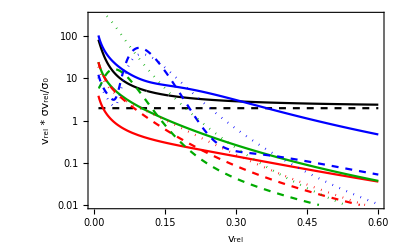

```mathematica
model="Co-annihilation with gluino";ζ=α3MZ/vrel;MDM=6000;group=SU3;gχ=16;
σ0=(π α3MZ^2)/MDM^2;Clear[σv,λ,CJ,CT,z,A,S];
λ[1]=3;dim[1]=1;
λ[8]=3/2;dim[8]=8; (* 8 is 8A *)
λ[9]=3/2;dim[9]=8; (* 9 is 8S *)
λ[10]=0.0001;dim[10]=10;
λ[27]=-1;dim[27]=27;
Somm[channel_]:=Sommerfeld[vrel/2,-λ[channel]α2MZ,MWT[MDM/z],MDM];
σv["ann"]=(27/32+9/8)σ0;σv["Sann"]=27/32 σ0(1/6 Somm[1]+1/3 Somm[8]+1/2 Somm[27])+9/8 σ0 Somm[8];
Attributes[CJ]={Orderless};
CJ[1,8]=√3;CT[1,8]=3 √(3/2);CT[8,1]=-CT[1,8];
CJ[8,9]=√6;CT[8,9]=0;CT[9,8]=0;
CJ[9,10]=2 √3;CT[9,10]=3 √3;CT[10,9]=-CT[9,10];
CJ[8,27]=3;CT[8,27]=15/2;CT[27,8]=-CT[8,27];
σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[{1,0,1,0}]=σvbsf[ζ,8->{1,0,1,0}];
σv[{8,1,1,0}]=σvbsf[ζ,1->{8,1,1,0}]+σvbsf[ζ,9->{8,1,1,0}]+σvbsf[ζ,27->{8,1,1,0}];
σv[{9,0,1,0}]=σvbsf[ζ,8->{9,0,1,0}]+σvbsf[ζ,10->{9,0,1,0}];
σv[{1,0,2,0}]=σvbsf[ζ,8->{1,0,2,0}];
σv[{8,1,2,0}]=σvbsf[ζ,1->{8,1,2,0}]+σvbsf[ζ,9->{8,1,2,0}]+σvbsf[ζ,27->{8,1,2,0}];
σv[{9,0,2,0}]=σvbsf[ζ,8->{9,0,2,0}]+σvbsf[ζ,10->{9,0,2,0}];
σv[{1,1,2,1}]=σvbsf[ζ,8->{1,1,2,1}];
σv[{8,0,2,1}]=σvbsf[ζ,1->{8,0,2,1}]+σvbsf[ζ,9->{8,0,2,1}]+σvbsf[ζ,27->{8,0,2,1}];
σv[{9,1,2,1}]=σvbsf[ζ,8->{9,1,2,1}]+σvbsf[ζ,10->{9,1,2,1}];
Γann[{1,0,1,0}]=243 α3MZ^5 MDM/4;
Γann[{8,1,1,0}]=243 α3MZ^5 MDM/64;
Γann[{9,0,1,0}]=243 α3MZ^5 MDM/128;
Γann[{1,0,2,0}]=243 α3MZ^5 MDM/32;
Γann[{8,1,2,0}]=243 α3MZ^5 MDM/512;
Γann[{9,0,2,0}]=243 α3MZ^5 MDM/1024;
Γann[{1,1,2,1}]=0;Γdecay[{1,1,2,1}]= α3MZ^6 MDM;
Γann[{8,0,2,1}]=0;Γdecay[{8,0,2,1}]=0.1 α3MZ^5 MDM;
Γann[{9,1,2,1}]=0;Γdecay[{9,1,2,1}]=0.1 α3MZ^5 MDM;
(* WARNING the values of the Gamma for the 8s and 8a states are inverted respect to the ones in the nb.of Michele. *)
Bstates={{1,0,1,0},{8,1,1,0},{9,0,1,0},{1,0,2,0},{8,1,2,0},{9,0,2,0},{1,1,2,1},{8,0,2,1},{9,1,2,1}};
Bnames={"1s_1","1s_(8_A)","1s_(8_S)","2s_1","2s_(8_A)","2s_(8_S)","2p_1","2p_(8_A)","2p_(8_S)"};
LogPlot[Evaluate[1/σ0 Join[{σv["ann"],σv["Sann"]/.z->25},Table[σv[this],{this,Bstates}]]],{vrel,0.01,0.6},FrameLabel->{"v_rel","v_rel * σv_rel/σ_0"},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,Join[{"Tree s-wave","Sommerfeld σv"},Bnames]],Right],Frame->True,PlotRange->{0.01,300},PlotStyle->{{Black,Dashed},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted}}]
```

### Squark

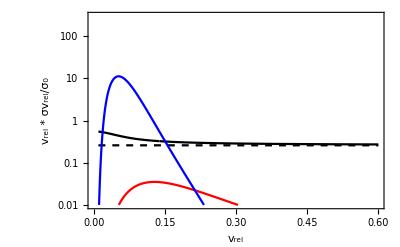

```mathematica
model="Co-annihilation with a squark";ζ=α3MZ/vrel;MDM=1500;group=SU3;gχ=6;
σ0=(π α3MZ^2)/MDM^2;Clear[σv,λ,CJ,CT,z,A,S];
λ[1]=4/3;dim[1]=1;
λ[8]=-1/6;dim[8]=8; 
Somm[channel_]:=Sommerfeld[vrel/2,-λ[channel]α2MZ,MWT[MDM/z],MDM];
σv["ann"]=7/27 σ0;σv["Sann"]=σv["ann"](2/7 Somm[1]+5/7 Somm[8]);
Attributes[CJ]={Orderless};CJ[1,8]=√(4/3);CT[1,8]=3/2 √(4/3);CT[8,1]=-CT[1,8];
σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[{1,0,1,0}]=σvbsf[ζ,8->{1,0,1,0}];
σv[{1,0,2,0}]=σvbsf[ζ,8->{1,0,2,0}];
σv[{1,0,2,1}]=σvbsf[ζ,8->{1,0,2,1}];
Γann[{1,0,1,0}]=32 α3MZ^5 MDM/81;
Γann[{1,0,2,0}]=4 α3MZ^5 MDM/81;
Γann[{8,0,2,1}]=0;Γdecay[{8,0,2,1}]= α3MZ^6 MDM;
Bstates={{1,0,1,0},{1,0,2,0}(*,{1,0,2,1}*)};
Bnames={"1s_1","2s_1","2p_1"};
LogPlot[Evaluate[1/σ0 Join[{σv["ann"],σv["Sann"]/.z->25},Table[σv[this],{this,Bstates}]]],{vrel,0.01,0.6},FrameLabel->{"v_rel","v_rel * σv_rel/σ_0"},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,Join[{"Tree s-wave","Sommerfeld σv"},Bnames]],Right],Frame->True,PlotRange->{0.01,300},PlotStyle->{{Black,Dashed},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted}}]
```

```mathematica
Table[σv[this],{this,Bstates}]/.vrel->0.1
```

{6.13593×10^-10,5.72059×10^-8,1.47625×10^-7}

### Make thermal averages

```mathematica
ztab=Table[10^lz,{lz,1,4,0.1}];zmax=Max[ztab];zmin=Min[ztab];
states=Join[{"ann","Sann"},Bstates];Clear[σvTtab];
Do[PrintTemporary[state];σvTtab[state]=ThermalAverage[state,group];,{state,states}];
σvTtab["tot"]=Sum[σvTtab[state],{state,Drop[states,1]}];
Do[σvTI[state]=Interpolation[Transpose[{ztab,σvTtab[state]}],InterpolationOrder->1],{state,Join[{"tot"},states]}];
Clear[BR,EB,EBQ,RσvTeff];
Do[DefineState[state];,{state,Bstates}];
RσvTeff["ann",z_]:=σvTI["ann"][z]/σ0;
RσvTeff["Sann",z_]:=σvTI["Sann"][z]/σ0;
RσvTeff["Btot",z_]:=Sum[RσvTeff[state,z],{state,Bstates}];
RσvTeff["tot",z_]:=RσvTeff["Sann",z]+RσvTeff["Btot",z];
```

Plot total σv without including BR

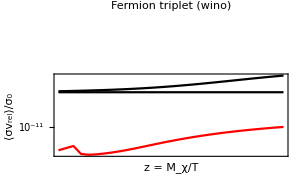
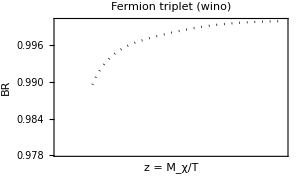

```mathematica
Row[{ListLinePlot[Table[Transpose[Log[10,{ztab,σvTtab[x]}]],{x,states}],Frame->True,FrameLabel->{"z = M_χ/T","⟨σv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[dettaglio1,normale],
PlotLegends->Join[{"σv_tree","S σv"},Table["σv("<>Bname<>")",{Bname,Bnames}]],PlotStyle->{{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model,Epilog->{Arrow[{{-1,-2.5},{2,-2.5}}],Text[" SU(2)_L unbroken ",{1.5,-2.5},Background->White]},ImageSize->300],
Plot[Evaluate[Table[BR[state,10^lz],{state,Bstates}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","BR"},
FrameTicks->LogLinTicks[dettaglio1],
PlotLegends->Table["BR("<>Bname<>")",{Bname,Bnames}],PlotStyle->{Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model,Epilog->{Arrow[{{-1,-2.5},{2,-2.5}}],Text[" SU(2)_L unbroken ",{1.5,-2.5},Background->White]},ImageSize->300]}]
```

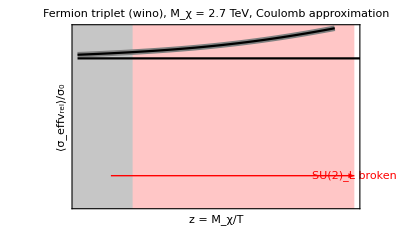

```mathematica
{xmin,xmax,ymin,ymax}={1,3,-2,1};plot5=Plot[Evaluate[Table[Log[10,RσvTeff[state,10^lz]],{state,Join[{"tot"},states]}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","⟨σ_effv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[normale],
Prolog->{If[group===SU2,{Lighter@Lighter@Pink,Rectangle[{Log[10,MDM/Tc],-4},{xmax,4}]},{}],Lighter@Lighter@Gray,Rectangle[{0,-4},{Log[10,25],4}]},
PlotLegends->Map[Style[#,Small,FontFamily->"Times"]&,Join[{"tot","tree","Som"},Bnames]],PlotStyle->{{Gray,Thickness[0.01]},{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model<>", M_χ = "<>ToString[MDM/1000.]<>" TeV, Coulomb approximation",PlotRange->{{xmin,xmax},{ymin,ymax}},Axes->False,
Epilog->If[group===SU2,{Red,Arrow[{{Log[10,MDM/Tc],ymin+0.5},{xmax,ymin+0.5}}],Text[" SU(2)_L broken ",{3,ymin+0.5},Background->Lighter@Lighter@Pink]},{}]]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/sigma5.pdf",plot5];
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/sigma8.pdf",plot5]
```

```mathematica
Export["/Users/astrumia/Dropbox/DM bound state/figs/sigmasquark.pdf",plot5]
```

/Users/astrumia/Dropbox/DM bound state/figs/sigmasquark.pdf

Above z > 10^4 the charged DM components gets Boltzmann suppressed by their ΔM

```mathematica
Clear[ΩDMhh];zmaxtab={zmax,1000,MDM/Tc};calcolatab={"Sann","tot"};
ΩDMhhtab=Table[λBoltz= σ0 MDM MPl  √(ndofSM π/45) ;Clear[zf];calcola=calcolatab⟦ic⟧;
zmaxeff=zmaxtab⟦iz⟧;
zf=zf/.FindRoot[zf==Log[2gχ RσvTeff[calcola,zf] λBoltz/((2π)^(3/2)Sqrt[zf])],{zf,25}];
YDM=1/λBoltz/(NIntegrate[RσvTeff[calcola,z]/z^2,{z,zf,zmaxeff},Method->{Automatic,"SymbolicProcessing"->0}]+RσvTeff[calcola,zf]/zf^2);
ΩDMhh[calcola,iz]=0.110 MDM YDM/(0.40 10^-9);
sPrint[ " Ω_DMh^2 = ",ΩDMhh[calcola,iz]," for σ = ",calcola," and {zf,zmax} = ",{zf,zmaxeff}];ΩDMhh[calcola,iz],{ic,{1,2}},{iz,{1,2,3}}];
Print["MDM = ",MDM" :  Ω_DMh^2 = ",TableForm[SetPrecision[ΩDMhhtab,3],TableHeadings->{calcolatab,zmaxtab}]]
```

MDM = 1500  :  Ω_DMh^2 =  | 10000. | 1000 | 9.67742
Sann | 0.0412 | 0.0431 | -0.0218
tot | 0.007 | 0.00917 | -0.0205

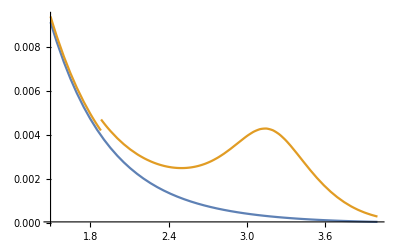

```mathematica
Plot[{RσvTeff["Sann",10^lz]/10^lz,RσvTeff["tot",10^lz]/10^lz},{lz,Log[10,zf],Log[10,zmax]},PlotRange->All]
```